# NG^4 T_03. Метод главных компонент

2 курс, 5 группа
Шклярик В.С.
20-фев-2023

## 1. Гистограмма.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Data = Import["NG23T03Problem.xlsx", {"Data", 1}]
```

{{Пол,1.,Standing (Стоя),,,,,, Sitting (Сидя),,,,,,,,,,,,, Hands (Ладонь),, Feet (Ступня),},{,,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.},759,{М,29.,1727.,1674.,1402.,1147.,777.,1920.,922.,765.,645.,247.,453.,132.,470.,581.,347.,783.,240.,353.,461.,183.,91.,258.,104.},{Ж,22.,1644.,1526.,1382.,1018.,701.,1901.,881.,741.,612.,242.,425.,149.,496.,558.,309.,721.,206.,389.,479.,193.,75.,238.,85.}}
 |  |  |  |

```mathematica
Data//Dimensions
```

{763,25}

```mathematica
Map[Dimensions,{Train, Test} = TakeDrop[RandomSample@#,Round[0.8 Length@#]]&@Data⟦5;;⟧]
```

{{607,25},{152,25}}

```mathematica
Map[Dimensions,{Train,Test}=TakeDrop[RandomSample@#,Round[0.8 Length@#]]&@Data[[5;;]]]
Map[Dimensions,{TrainLabel,Train}={Train[[All,1]],Train[[All,2;;]]}]
Map[Dimensions,{TestLabel,Test}={Test[[All,1]],Test[[All,2;;]]}]
```

{{607,25},{152,25}}

{{607},{607,24}}

{{152},{152,24}}

```mathematica
Length[indMale = Flatten@Position[TrainLabel, "М"]]
```

305

```mathematica
Length[indFemale = Flatten@Position[TrainLabel, "Ж"]]
```

302

```mathematica
age = Data⟦5;;, 2⟧;
names = Data⟦4, 2;;⟧;
nameNums = Data⟦2, 3;;⟧;
```

```mathematica
Data⟦4;;,3⟧;
```

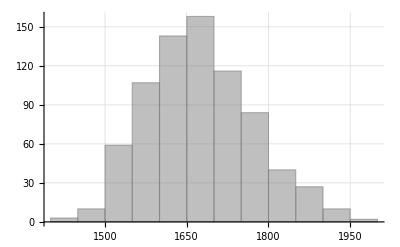

```mathematica
Histogram[{Data⟦4;;,3⟧},GridLines->Automatic,ChartStyle->Gray]
```

```mathematica
Data⟦5;;,2;;⟧⟦indMale,24⟧;
```

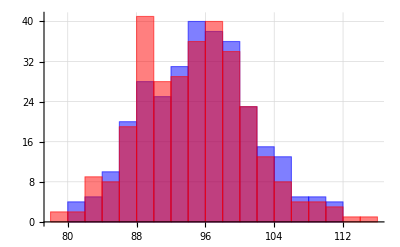

```mathematica
Histogram[{Data⟦5;;,2;;⟧⟦indFemale,24⟧,Data⟦5;;,2;;⟧⟦indMale,24⟧},GridLines->Automatic,ChartStyle->{Blue,Red}]
```

```mathematica
Manipulate[{Histogram[{Data⟦4;;,Параметр+1⟧},30,GridLines->Automatic,ChartStyle->Gray,PlotLabel->names⟦Параметр⟧], Histogram[{Data⟦5;;,2;;⟧⟦indMale,Параметр⟧,Data⟦5;;,2;;⟧⟦indFemale,Параметр⟧},30,GridLines->Automatic,ChartStyle->{Blue,Red},PlotLabel->names⟦Параметр⟧]}⟦Пол⟧,{Пол,{ 1->"Все",2-> "М/Ж"}}, {Параметр,Range[2,24]},ControlType->SetterBar, ControlPlacement->Top]
```

## 2. Стандартизация данных

```mathematica
Dimensions[Stat = Through@{Mean, StandardDeviation}@Train]
```

{2,24}

```mathematica
Stat⟦All,11⟧
```

{233.47,26.3288}

```mathematica
Dimensions[stdTrain =MapThread[ (#1 - First@#2)/(Last@#2)&, {Trainᵀ, Statᵀ}]ᵀ]
```

{607,24}

```mathematica
Through@{Mean, StandardDeviation}@stdTrain
%//Chop
```

{{-6.73084×10^-17,-8.77936×10^-17,1.69734×10^-16,8.1648×10^-16,2.24605×10^-16,1.03999×10^-15,-3.04351×10^-16,4.15556×10^-16,1.21448×10^-15,-1.47786×10^-16,5.27859×10^-16,-1.46323×10^-16,-7.89776×10^-16,-8.57451×10^-16,-3.34347×10^-16,4.24336×10^-16,2.86792×10^-16,-2.66307×10^-16,-5.17616×10^-16,-3.74586×10^-16,1.05352×10^-16,-5.85291×10^-16,6.31382×10^-16,-4.00924×10^-16},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

## 3. Ковариационная матрица.

```mathematica
{MatrixPlot[Cov = Covariance@Train, ImageSize->200, ColorFunction->"GreenPinkTones"], MatrixPlot[stdCov = Covariance@stdTrain, ImageSize->200, ColorFunction->"GreenPinkTones"]};
```

```mathematica
ClearAll[kmMatrixPlot];
kmMatrixPlot[M_, opts___]:=MatrixPlot[Rescale[M,{-#,#}&@Max@Abs@M],ColorFunctionScaling->False, LabelStyle->Black,ColorFunction->(If[0.49<#<0.51,White,ColorData["GreenPinkTones",#]]&),opts]
```

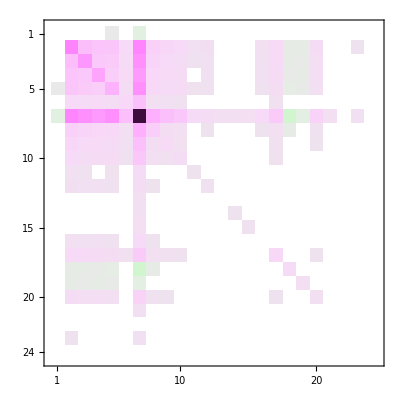
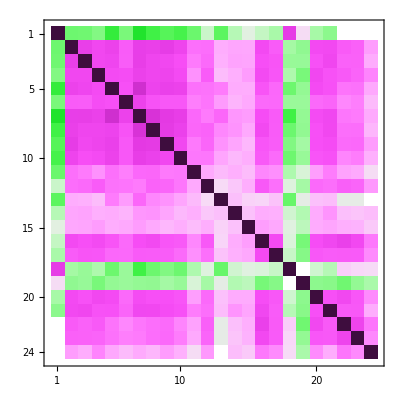

```mathematica
{kmMatrixPlot[Cov],kmMatrixPlot[stdCov]}
```

## 4. «Правило трёх сигм»

```mathematica
Flatten@{-∞, μ+Range[-3,3] σ, ∞}
```

{-∞,μ-3 σ,μ-2 σ,μ-σ,μ,μ+σ,μ+2 σ,μ+3 σ,∞}

```mathematica
intPerc = {Assuming[And[σ>0,μ∈Reals],∫_(-∞)^(μ-3 σ) 1/(σ √(2 π))ⅇ^((-(x-μ)^2)/(2 σ^2))ⅆx]//N,Assuming[And[σ>0,μ∈Reals],∫_(μ-3 σ)^(μ-2 σ) 1/(σ √(2 π))ⅇ^((-(x-μ)^2)/(2 σ^2))ⅆx]//N,Assuming[And[σ>0,μ∈Reals],∫_(μ-2 σ)^(μ- σ) 1/(σ √(2 π))ⅇ^((-(x-μ)^2)/(2 σ^2))ⅆx]//N,Assuming[And[σ>0,μ∈Reals],∫_(μ-σ)^μ 1/(σ √(2 π))ⅇ^((-(x-μ)^2)/(2 σ^2))ⅆx]//N}
```

{0.0013499,0.0214002,0.135905,0.341345}

```mathematica
iperc =Join[PercentForm/@intPerc,PercentForm/@ Reverse@intPerc]
```

{0.135%,2.14%,13.59%,34.13%,34.13%,13.59%,2.14%,0.135%}

```mathematica
Stat⟦All,1⟧;
Flatten@{-∞, First@%+Range[-3,3] Last@%, ∞};
N@BinCounts[Train⟦All, 1⟧, {%}]/Length@Train;
perc = PercentForm[#, {∞, 2}]&/@%
```

{0.00%,0.00%,19.60%,25.70%,36.57%,18.12%,0.00%,0.00%}

```mathematica
Train⟦All,1⟧;
```

```mathematica
Statᵀ⟦1⟧
```

{55.0593,17.0722}

```mathematica
PDF[NormalDistribution@@(Statᵀ⟦1⟧),x]
```

0.023368 ⅇ^(-0.00171551 (-55.0593+x)^2)

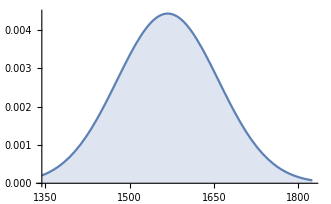

```mathematica
F = Plot[PDF[NormalDistribution@@(Statᵀ⟦3⟧),x], {x,Min@Train⟦All,3⟧,Max@Train⟦All,3⟧}, Filling->Bottom]
```

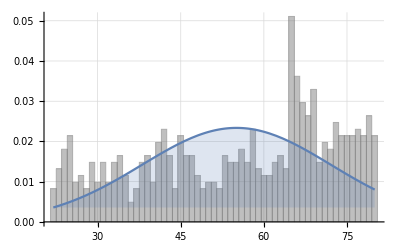

```mathematica
Show[Histogram[{Train⟦All,1⟧},50,"PDF",GridLines->Automatic,ChartStyle->Gray],Plot[PDF[NormalDistribution@@(Statᵀ⟦1⟧),x], {x,Min@Train⟦All,1⟧,Max@Train⟦All,1⟧}, Filling->Bottom]]
```

```mathematica
Manipulate[Show[Histogram[{Train⟦All,Параметр⟧},50,"PDF",GridLines->Automatic,ChartStyle->Gray,PlotLabel->Column[{Grid[{{-∞,μ-3 σ,μ-2 σ,μ-σ,μ,μ+σ,μ+2 σ,μ+3 σ,∞}}, Frame->All, Background->Black, ItemStyle->White], 
Grid[{ iperc, PercentForm[#, {∞, 2}]&/@N@(BinCounts[Train⟦All, Параметр⟧, {Flatten@{-∞, First@Stat⟦All,Параметр⟧+Range[-3,3] Last@Stat⟦All,Параметр⟧, ∞}}]/Length@Train)}, Frame->All]}, Center], ImageSize->{600,400}],Plot[PDF[NormalDistribution@@(Statᵀ⟦Параметр⟧),x], {x,Min@Train⟦All,Параметр⟧,Max@Train⟦All,Параметр⟧}, Filling->Bottom]], {Параметр,Range[1,24]},ControlType->SetterBar, ControlPlacement->Top,ContentSize->Automatic]
```

## 5. Эллипсоид рассеивания.

```mathematica
{11,19};
Through@{Mean, Covariance}@Train⟦All, %⟧
```

{{233.47,389.773},{{693.207,-82.5251},{-82.5251,1233.52}}}

{{233.47,389.773},{{693.207,-82.5251},{-82.5251,1233.52}}}

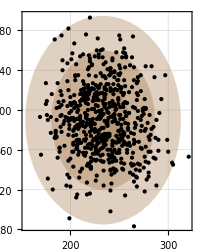

```mathematica
{11,19};
Through@{Mean, Covariance}@Train⟦All, %⟧
Graphics[{Opacity[.3, Brown],Ellipsoid@@%,Apply[Ellipsoid [#1,4#2]&,%],Apply[Ellipsoid [#1,9#2]&,%],PointSize@Small,Opacity[1,Black], Black, Point@Train⟦All,%%⟧}, Frame->True, ImageSize->200, GridLines->Automatic]
```

{{-7.68194×10^-17,5.63708×10^-16},{{1.,-0.361829},{-0.361829,1.}}}

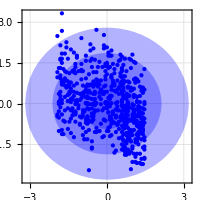

```mathematica
{1,11};
Through@{Mean, Covariance}@stdTrain⟦All, %⟧
Graphics[{Opacity[.3, Blue],Ellipsoid@@%,Apply[Ellipsoid [#1,4#2]&,%],Apply[Ellipsoid [#1,9#2]&,%],PointSize@Small,Opacity[1,Blue], Point@stdTrain⟦All,%%⟧}, Frame->True, ImageSize->200, GridLines->Automatic]
```

```mathematica
ClearAll[MS, stdMS];
stdMS[{h_,v_}]:=Through@{Mean, Covariance}@stdTrain⟦All, {h,v}⟧;
MS[{h_,v_}]:=Through@{Mean, Covariance}@Train⟦All, {h,v}⟧;
Manipulate[Row[{Graphics[{Opacity[.3, Brown],Apply[Ellipsoid,MS[{1,11}]],Apply[Ellipsoid [#1,4#2]&,MS[{1,11}]],Apply[Ellipsoid [#1,9#2]&,MS[{1,11}]],PointSize@Small,Opacity[1,Black], Black, Point@Train⟦All,{1,11}⟧}, Frame->True, ImageSize->200, GridLines->Automatic,FrameLabel->{names⟦гор⟧,names⟦вер⟧}, PlotLabel->"Исходные данные"],
Graphics[{Opacity[.3, Blue],Ellipsoid@@stdMS[{гор,вер}],Apply[Ellipsoid [#1,4#2]&,stdMS[{гор,вер}]],Apply[Ellipsoid [#1,9#2]&,stdMS[{гор,вер}]],PointSize@Small,Opacity[1,Blue], Point@stdTrain⟦All,{гор,вер}⟧}, Frame->True, ImageSize->200, GridLines->Automatic,FrameLabel->{names⟦гор⟧,names⟦вер⟧}, PlotLabel->"Стандартизованные данные"]} , "\t"],{гор,Range[24]}, {вер,Range[24]},ControlType->SetterBar, ControlPlacement->Top]
```

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{1.,1.},{1.,1.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition::posdef: The matrix {{4.,4.},{4.,4.}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

## 6.Сингулярное разложение матрицы

```mathematica
Map[Dimensions,{U,S,V} = SingularValueDecomposition@Train]
```

{{607,607},{607,24},{24,24}}

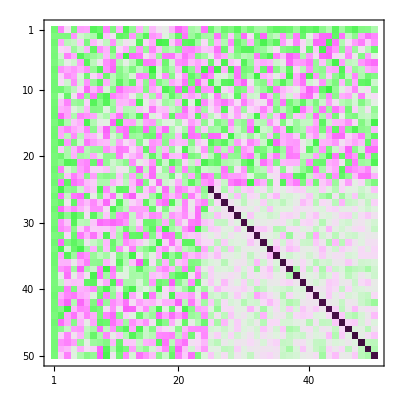
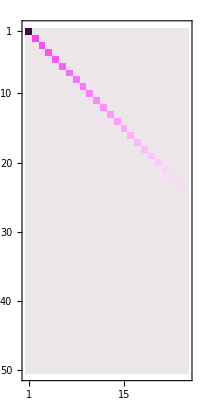
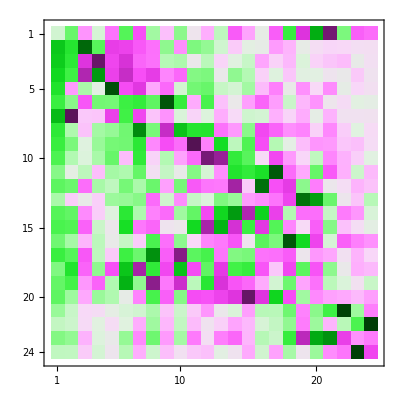

```mathematica
MatrixPlot[#, ImageSize->{Automatic,150}, ColorFunction->"GreenPinkTones"]&/@{Take[U,50,50],Take[S,50],V}
```

```mathematica
MinMax[Train-U.S.Vᵀ]
```

{-3.75167×10^-12,2.31921×10^-11}

```mathematica
Map[Dimensions,{stdU,stdS,stdV} = SingularValueDecomposition@stdTrain]
```

{{607,607},{607,24},{24,24}}

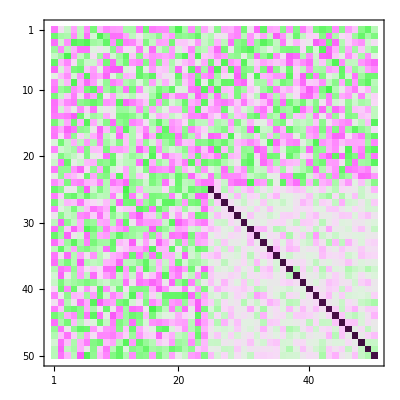
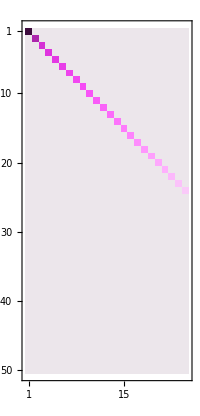
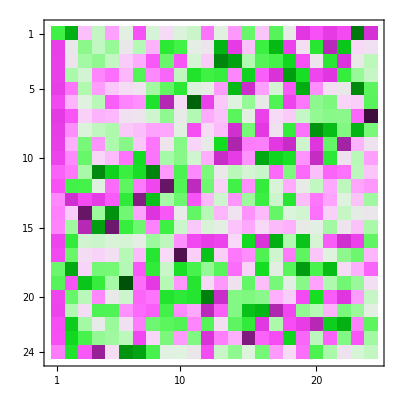

```mathematica
MatrixPlot[#, ImageSize->{Automatic,150}, ColorFunction->"GreenPinkTones"]&/@{Take[stdU,50,50],Take[stdS,50],stdV}
```

```mathematica
MinMax[stdTrain-stdU.stdS.stdVᵀ]
```

{-1.90958×10^-14,1.76525×10^-14}

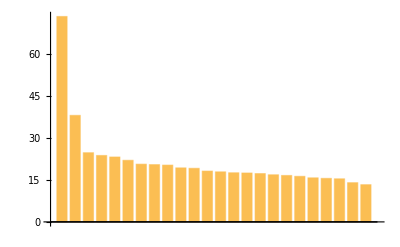

```mathematica
BarChart[Diagonal@stdS]
```

```mathematica
Take[stdS, 24]⟦2,2⟧
```

38.1033

```mathematica
Dimensions[stdU]
stdU⟦All,1;;24⟧
```

{607,607}

{{0.0524517,0.00252298,-0.0100601,0.0236661,-0.0124926,0.0393312,-0.0496447,0.0148582,0.0405079,0.0288557,0.0270405,-0.0211311,-0.0215545,0.0506011,-0.053063,0.0485684,0.0402554,0.0384036,-0.0299182,-0.101934,-0.0207133,0.0359023,-0.0320072,0.0230021},605,{-0.0583332,-0.0204282,0.065192,0.0180854,-0.000435359,0.0832966,-0.0657852,-0.0419995,8,-0.0783569,0.0239942,0.0146855,0.0345125,0.0132177,-0.0276455,0.00190753,0.0153773}}
 |  |  |  |

```mathematica
stdTrain-stdU⟦All,1;;3⟧.stdS⟦1;;3,1;;3⟧.stdV⟦All,1;;3⟧ᵀ
```

{{-0.234146,-0.108297,-0.492999,0.38568,-0.521002,-0.084687,0.311211,1.61476,0.721106,-0.993796,-0.261836,0.152109,-1.31371,-0.283329,-0.539674,0.322319,0.427485,-0.0915726,-0.949751,-0.0371514,0.120453,-0.860407,-1.18803,0.310644},605,{0.150745,0.822451,-0.760274,-0.0738443,0.175362,0.410524,0.29811,-0.505845,-0.68783,6,0.437598,-0.148758,-0.262635,-1.35678,0.375929,-0.44938,0.737534,-0.886997,-0.197743}}
 |  |  |  |

```mathematica
Norm[#]&@(stdTrain-stdU⟦All,1;;3⟧.stdS⟦1;;3,1;;3⟧.stdV⟦All,1;;3⟧ᵀ)
```

23.7557

```mathematica
PercentForm[(Norm[#]&@(stdTrain-stdU⟦All,1;;1⟧.stdS⟦1;;1,1;;1⟧.stdV⟦All,1;;1⟧ᵀ))/Norm[stdTrain]]
```

51.87%

```mathematica
Grid[Prepend[Chop@Table[{n,Take[stdS, 24]⟦n,n⟧,Min[#], Max[#],  Norm[#],PercentForm[ Min[#]/Norm[stdTrain],{∞,2}],PercentForm[Max[#]/Norm[stdTrain],{∞,2}],PercentForm[Norm[#]/Norm[stdTrain], {∞,2}]}&@(stdTrain-stdU⟦All,1;;n⟧.stdS⟦1;;n,1;;n⟧.stdV⟦All,1;;n⟧ᵀ),{n,1,24}],{"n", "SV", "∆_min", "∆_max", "∆", "δ_min", "δ_max", "δ"}], Frame->All,Background->{{LightGreen},{LightGray}}]
```

n | SV | ∆_min | ∆_max | ∆ | δ_min | δ_max | δ
1 | 73.4656 | -2.91931 | 3.21939 | 38.1033 | -3.97% | 4.38% | 51.87%
2 | 38.1033 | -2.99154 | 2.90843 | 24.7469 | -4.07% | 3.96% | 33.68%
3 | 24.7469 | -2.72719 | 2.73125 | 23.7557 | -3.71% | 3.72% | 32.34%
4 | 23.7557 | -2.62477 | 2.6595 | 23.2205 | -3.57% | 3.62% | 31.61%
5 | 23.2205 | -2.57921 | 2.56549 | 22.0354 | -3.51% | 3.49% | 29.99%
6 | 22.0354 | -2.74538 | 2.55098 | 20.6533 | -3.74% | 3.47% | 28.11%
7 | 20.6533 | -2.85616 | 2.59309 | 20.4894 | -3.89% | 3.53% | 27.89%
8 | 20.4894 | -2.54478 | 2.55821 | 20.3185 | -3.46% | 3.48% | 27.66%
9 | 20.3185 | -2.41002 | 2.37878 | 19.326 | -3.28% | 3.24% | 26.31%
10 | 19.326 | -2.41909 | 2.30303 | 19.1716 | -3.29% | 3.13% | 26.10%
11 | 19.1716 | -2.32507 | 2.24264 | 18.1805 | -3.16% | 3.05% | 24.75%
12 | 18.1805 | -2.3774 | 2.24298 | 17.9053 | -3.24% | 3.05% | 24.37%
13 | 17.9053 | -2.27958 | 2.15497 | 17.5736 | -3.10% | 2.93% | 23.92%
14 | 17.5736 | -2.32548 | 2.16002 | 17.497 | -3.17% | 2.94% | 23.82%
15 | 17.497 | -1.83076 | 2.07252 | 17.2831 | -2.49% | 2.82% | 23.53%
16 | 17.2831 | -1.69413 | 1.78376 | 16.8539 | -2.31% | 2.43% | 22.94%
17 | 16.8539 | -1.77605 | 1.51739 | 16.61 | -2.42% | 2.07% | 22.61%
18 | 16.61 | -1.78147 | 1.47893 | 16.2979 | -2.42% | 2.01% | 22.18%
19 | 16.2979 | -1.88241 | 1.41683 | 15.7635 | -2.56% | 1.93% | 21.46%
20 | 15.7635 | -1.84293 | 1.38626 | 15.573 | -2.51% | 1.89% | 21.20%
21 | 15.573 | -1.65038 | 1.22217 | 15.4159 | -2.25% | 1.66% | 20.98%
22 | 15.4159 | -1.30242 | 1.3152 | 14.0303 | -1.77% | 1.79% | 19.10%
23 | 14.0303 | -1.29286 | 1.28133 | 13.3157 | -1.76% | 1.74% | 18.13%
24 | 13.3157 | 0 | 0 | 0 | 0% | 0% | 0%

Как сингулярное разложение может помочь сэкономить память?
Из формулы (6) следует, что для задания матрицы М размера m x n и ранга r,  достаточно хранить в памяти (mr (матрица U) + nr (матрица V) + r (матрица S)) чисел. 
Получим, что память можно сэкономить, если mn>r(m+n+1). Матрицы, для которых данное неравенство верно, существуют, например квадратная матрица n x n с рангом r < n^2/(2n+1).

## 7. Выделение главных компонент.

```mathematica
Dimensions[pcTrain =stdTrain.V]
```

{607,24}

```mathematica
stdTrain⟦123⟧.V
```

{-2.18577,-0.318372,-0.0797282,-1.13916,-1.55495,1.19274,-0.840368,0.745528,0.048919,0.996953,1.46629,0.687899,0.489508,0.29716,0.946155,-0.121906,0.177158,-1.71401,0.201289,0.755006,-1.61027,-0.222944,-0.109875,0.688577}

```mathematica
Dimensions[μσ =Through@{Mean, StandardDeviation}@pcTrain]
```

{2,24}

```mathematica
Dimensions[covar = Covariance@pcTrain]
```

{24,24}

```mathematica
Dimensions[μσ⟦2⟧]
```

{24}

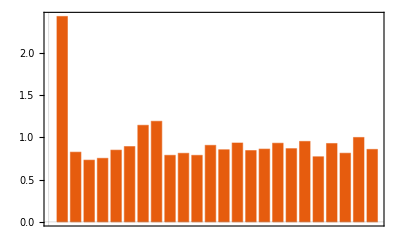

```mathematica
BarChart[μσ⟦2⟧, PlotTheme->"Scientific"]
```

## 8. Hаивный байесовский классификатор.

```mathematica
ClearAll[W1];
W1[x_, n_] :=(MapThread[(#1 -First@#2)/(Last@#2)&, {x,μσᵀ}].V)⟦1;;n⟧
```

```mathematica
Dimensions[W1[Test⟦21⟧,8]]
```

{8}

```mathematica
StatFemale = Mean@pcTrain⟦indFemale, #⟧&/@Range[24];
StatMale = Mean@pcTrain⟦indMale, #⟧&/@Range[24];
```

```mathematica
StatFemale
```

{1.8051,0.359863,-0.150994,0.228114,0.182248,-0.162548,0.252054,0.835722,-0.059727,0.228438,-0.276798,-0.347309,-0.0566126,-0.284356,-0.229949,0.297532,0.306171,0.470059,-0.148502,0.207666,0.385983,0.289069,0.478863,0.537882}

```mathematica
Dimensions[preW2 = Inverse[covar].(StatFemale-StatMale)]
```

{24}

```mathematica
W02 = 1/2(StatMale.Inverse[covar].StatMale -StatFemale.Inverse[covar].StatFemale)
```

-0.00861649

```mathematica
W2 = Append[preW2, W02]
```

{0.427448,0.39321,-0.0630517,0.0970208,-0.0307359,-0.0181944,-0.0782113,0.276023,-0.077732,0.151522,-0.177033,-0.0654666,-0.127488,-0.183201,-0.0222105,0.129137,0.0414715,0.201717,-0.258744,0.129247,-0.122731,0.0400256,0.174806,0.305705,-0.00861649}

Когда я считала w_0 по формуле  w_0==1/2(OverVector[μ_Male]·C^-1·OverVector[μ_Male]-OverVector[μ_Female]·C^-1·OverVector[μ_Female]) , то ничего не получалось, классификатор выдавал нули на все тестовые образцы.
Далее я считаю w_0 по формуле mean_(x∈Female) NBC[x]==0 из прошлой работы.

```mathematica
Clear[W2, W0];
W2[n_]:= (Inverse[covar].(StatFemale-StatMale))⟦1;;n⟧
W0[n_]:= -Mean@Table[W2[n].W1[Train⟦i⟧,n],{i,indFemale}]
```

```mathematica
ClearAll[NBC];
NBC[x_, n_]:=UnitStep[Append[W2[n],W0[n]].Append[W1[x,n],1]]
```

```mathematica
TestLabel
```

{М,Ж,М,М,Ж,Ж,М,Ж,Ж,Ж,Ж,М,М,Ж,М,Ж,М,Ж,Ж,М,М,М,Ж,Ж,М,Ж,М,Ж,М,Ж,Ж,М,Ж,М,Ж,М,Ж,Ж,Ж,Ж,М,Ж,М,Ж,Ж,М,М,М,Ж,Ж,Ж,Ж,Ж,М,Ж,М,Ж,М,Ж,М,М,Ж,М,М,М,М,М,Ж,Ж,М,Ж,М,Ж,М,Ж,Ж,Ж,М,М,Ж,М,М,Ж,Ж,Ж,Ж,Ж,М,М,Ж,Ж,М,М,М,М,Ж,М,Ж,М,М,М,Ж,М,М,М,Ж,М,М,Ж,М,Ж,М,Ж,Ж,М,М,Ж,М,М,Ж,М,Ж,Ж,М,М,Ж,М,Ж,Ж,Ж,Ж,М,Ж,Ж,Ж,М,Ж,М,Ж,М,Ж,Ж,М,Ж,М,М,Ж,Ж,М,М,Ж,Ж}

```mathematica
NBC[Test⟦8⟧,5]
```

1

```mathematica
test2NBC = NBC[#,2]&/@Test
```

{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,0,1,0,0,1,0,1,1,1,1,0,1,1,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1}

```mathematica
Er12 = PercentForm[N@(Count[test2NBC⟦indF⟧,0]/Length[indF])]
```

55.7%

```mathematica
Er22 = PercentForm[N@(Count[test2NBC⟦indM⟧,1]/Length[indM])]
```

1.37%

```mathematica
Er11 = PercentForm[N@(Count[(NBC[#,1]&/@Test)⟦indF⟧,0]/Length[indF])];
Er21 = PercentForm[N@(Count[(NBC[#,1]&/@Test)⟦indM⟧,1]/Length[indM])];
Er13 = PercentForm[N@(Count[(NBC[#,3]&/@Test)⟦indF⟧,0]/Length[indF])];
Er23 = PercentForm[N@(Count[(NBC[#,3]&/@Test)⟦indM⟧,1]/Length[indM])];
Er15 = PercentForm[N@(Count[(NBC[#,5]&/@Test)⟦indF⟧,0]/Length[indF])];
Er25 = PercentForm[N@(Count[(NBC[#,5]&/@Test)⟦indM⟧,1]/Length[indM])];
Er111 = PercentForm[N@(Count[(NBC[#,11]&/@Test)⟦indF⟧,0]/Length[indF])];
Er211 = PercentForm[N@(Count[(NBC[#,11]&/@Test)⟦indM⟧,1]/Length[indM])];
```

```mathematica
Grid[{{"Главных компонент", "Женщину за мужчину", "Мужчину за женщину"},{1, Er11, Er21},{2, Er12, Er22}, {3, Er12, Er23},{5, Er15, Er25}, {11,Er111,Er211}}, Frame->All, Background->{{LightGreen},{LightGray}}]
```

Главных компонент | Женщину за мужчину | Мужчину за женщину
1 | 62.03% | 0%
2 | 55.7% | 1.37%
3 | 55.7% | 0%
5 | 55.7% | 1.37%
11 | 55.7% | 0%